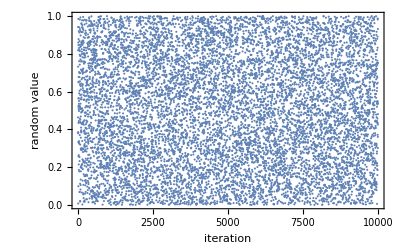

```mathematica
n=10000;
rlist=Table[Random[],{i,1,n}];
Show[ListPlot[rlist,Frame->True,FrameLabel->{"iteration","random value"}]]
(* the plot looks uniform, but how do we compute the distribution? For a uniform distribution, we expect P(x) to be independent of x.  So, lets put the random values into bins.  *)
```

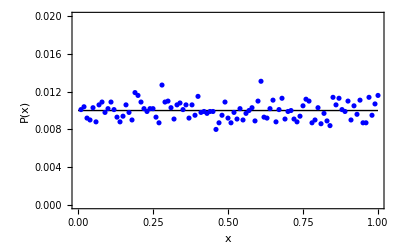

```mathematica
nbin=100;
bins=Table[{i/100,0},{i,1,nbin}];
Do[
rval=rlist[[i]];  (*pick a random value to bin *)
Do[
If[rval<bins[[j,1]],  (* if that random value is smaller than the current bin,*)
bins[[j,2]]+=1./n;  (* put it into the bin *)
Break[] (* once we found its bin, stop! *)
];
,{j,1,nbin}];  (* search over all bins *)

,{i,1,n}]; (* check all numbers *)
p1=ListPlot[bins,PlotStyle->Blue];  (* plot the data *)
p2=Plot[1/nbin,{x,0,1},PlotStyle->{Black,Thick}];  (* plot the expected value *)
Show[p2,p1,Frame->True,Axes->False,FrameLabel->{"x","P(x)"}]  (*compare them *)
```

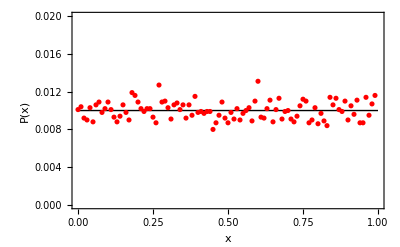

```mathematica
bins2=Tally[IntegerPart[nbin * rlist]];  (* assign the bins by taking the integer part *)
Do[
bins2[[i,1]]/=nbin;  (* rescale the x and y axes *) 
bins2[[i,2]]/=n;
,{i,1,Length[bins2]}];
p1=ListPlot[bins2,PlotStyle->Red]; (* plot them *)
p2=Plot[1/nbin,{x,0,1},PlotStyle->{Black,Thick}];
Show[p2,p1,Frame->True,Axes->False,FrameLabel->{"x","P(x)"}]
```

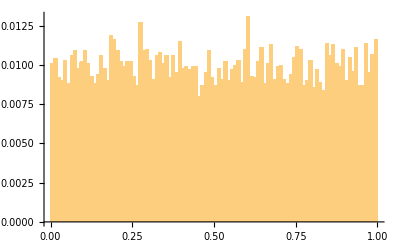

```mathematica
Histogram[rlist,nbin,"Probability"]  (* fully automated, but not too useful *)
```

```mathematica
(* to quanitfy the goodness of a distribution, we can use the Kolmogorov-Smirnov test  (no relation to the Smirnoff vodka).  

This effectively compares the largest deviation from the observed to the tested deviation.  A large deviation is unlikely by random chance.  The test returns the probability that that the data has the tested distribution (called the null hypothesis) is false.  

Small values are good.  below 5% is a typical value for statistical significance.  Some authors use "strongly significant" below 0.5%.  Recently a debate has occured arguing 5% is far too high for inference.  

*)

Print["statistic for uniform on [0,1):  ",KolmogorovSmirnovTest[rlist,UniformDistribution[{0,1}],"PValue"]]
(* this is the probability that the null hypothesis (the data does not come from the uniform distribution between 0-1) is FALSE.  Large values are better than small values.  *)

Print["statistic for uniform on [0,3):  ",KolmogorovSmirnovTest[rlist,UniformDistribution[{0,3}],"PValue"]]
(* This depends on both the distribution (uniform) and the ra  *)
```

statistic for uniform on [0,1):  0.650792

General::munfl: Exp[-8889.37] is too small to represent as a normalized machine number; precision may be lost.

statistic for uniform on [0,3):  0.

```mathematica
KolmogorovSmirnovTest[rlist,UniformDistribution[{0,1}],"TestConclusion"]
```

The null hypothesis that the data is distributed according to the UniformDistribution[{0,1}] is not rejected at the 5 percent level based on the Kolmogorov-Smirnov test.

```mathematica
KolmogorovSmirnovTest[rlist,UniformDistribution[{0,1}],"ShortTestConclusion"]
KolmogorovSmirnovTest[rlist,UniformDistribution[{0,3}],"ShortTestConclusion"]
```

Do not reject

General::munfl: Exp[-8889.37] is too small to represent as a normalized machine number; precision may be lost.

Reject